# BMV Dataset builder

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"EconomicComputations.wl"}]];
```

```mathematica
CreateDatabaseFromYahooFile[path_]:=Block[{dataset,dates,prices},
dataset = Import[path];
dates = Map[DateObject,Drop[dataset[[All,1]],1]];
prices = Drop[dataset[[All,5]],1];
Transpose[{dates,prices}]
];
```

```mathematica
GetPriceAtDate[dataset_,date_]:=Block[{pos},
pos = FirstPosition[dataset,{date,_}];
If[pos =!=Missing["NotFound"],Last[Extract[dataset,pos]],None]
];
GetPricesFromDatasetAtDate[dataset_,date_]:=Table[GetPriceAtDate[currentDataset,date],{currentDataset,dataset}];
```

```mathematica
FormatPrices[prices_]:=Block[{propagateBackwards,propagateForward},
propagateBackwards = FixedPoint[
SequenceReplace[#,
{
{"null",x_ /;NumberQ[x]}:>Sequence[x,x],
{None,x_ /;NumberQ[x]}:>Sequence[x,x]
}
]&,
prices
];
propagateForward = FixedPoint[
SequenceReplace[#,
{
{x_ /;NumberQ[x],"null"}:>Sequence[x,x],
{x_ /;NumberQ[x],None}:>Sequence[x,x],
{x_ /;NumberQ[x],""}:>Sequence[x,x]
}
]&,
propagateBackwards
];
Return[propagateForward];
];
CreateDatabase[date_]:=Block[{files,stocks,dataset,availableDates,datedDatabase,pricesByStock,stringDates,processed,processedPrices,toExport},
files = FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV",date}]];
stocks = Map[FileBaseName,files];
dataset = ProgressParallelMap[CreateDatabaseFromYahooFile,files];
availableDates = Sort@DeleteDuplicates[Flatten[dataset[[All,All,1]]]];
datedDatabase =ProgressMap[{#,GetPricesFromDatasetAtDate[dataset,#]}&,availableDates];
pricesByStock = Transpose@datedDatabase[[All,2]];
stringDates = ProgressMap[DateString[#,"ISODateTime"]&,datedDatabase[[All,1]]];
processed = ProgressMap[FormatPrices,pricesByStock];
processedPrices = Transpose[processed];
toExport = Thread[{stringDates,processedPrices}];
Export[FileNameJoin[{NotebookDirectory[],"BMV",date<>".wdx"}],toExport];
Export[FileNameJoin[{NotebookDirectory[],"BMV",date<>".csv"}],Join[{stocks},processedPrices]];
Export[FileNameJoin[{NotebookDirectory[],"BMV",date<>"_dates.csv"}],stringDates];
];
```

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders];
```

```mathematica
dates
```

{20-01-2020,21-01-2020,22-01-2020,23-01-2020,24-01-2020,27-01-2020,28-01-2020,29-01-2020}

```mathematica
ProgressMap[CreateDatabase,{"24-01-2020","27-01-2020","28-01-2020","29-01-2020"}]
```

{Null,Null,Null,Null}

```mathematica
CreateDatabase[Last[dates]]
```

### Names

```mathematica
files = FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV",dates[[3]]}]];
stocks = Map[FileBaseName,files];
```

```mathematica
stocks
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

## Shit

```mathematica
files = FileNames["*",FileNameJoin[{NotebookDirectory[],"BMV",First[dates]}]];
```

```mathematica
stocks = Map[FileBaseName,files];
```

```mathematica
stocks
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
dataset = ProgressParallelMap[CreateDatabaseFromYahooFile,files];
```

```mathematica
availableDates = Sort@DeleteDuplicates[Flatten[dataset[[All,All,1]]]];
```

```mathematica
GetPricesFromDatasetAtDate[dataset,DateObject[{2020,1,20,14,54,0},"Instant","Gregorian",-6.]]
```

{105.74,21.62,49.38,15.52,389.89,32.01,36.04,,28.06,7.73,34.15,238.5,74.98,,21.04,113.79,57.82,204.98,87.51,41.05,116.75,20.37,102.,76.59,149.55,48.65,204.74,205.05,111.66,46.83}

```mathematica
datedDatabase =ProgressMap[{#,GetPricesFromDatasetAtDate[dataset,#]}&,availableDates];
```

```mathematica
pricesByStock = Transpose@datedDatabase[[All,2]];
```

```mathematica
stringDates = ProgressMap[DateString[#,"ISODateTime"]&,datedDatabase[[All,1]]];
```

```mathematica
processed = ProgressMap[FormatPrices,pricesByStock];
```

```mathematica
processedPrices = Transpose[processed];
```

```mathematica
toExport = Thread[{stringDates,processedPrices}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"BMV",First[dates]<>".wdx"}],toExport];
Export[FileNameJoin[{NotebookDirectory[],"BMV",First[dates]<>".csv"}],processedPrices];
Export[FileNameJoin[{NotebookDirectory[],"BMV",First[dates]<>"_dates.csv"}],stringDates];
```

```mathematica
onlyDates = toExport[[All,1]];
onlyPrices = toExport[[All,2]];
```

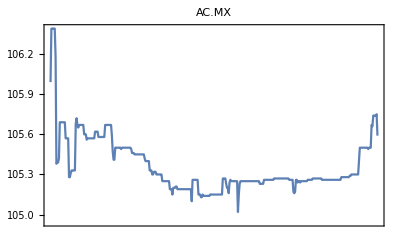
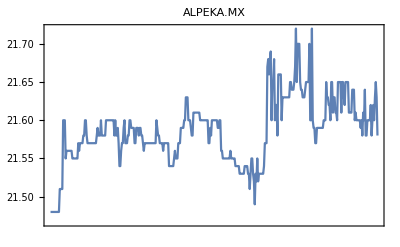
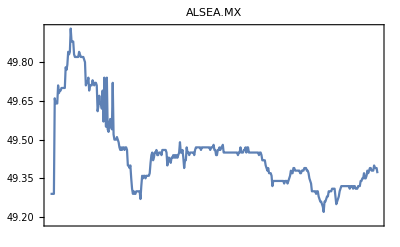
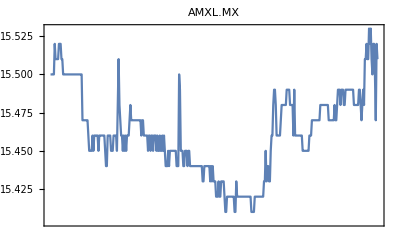
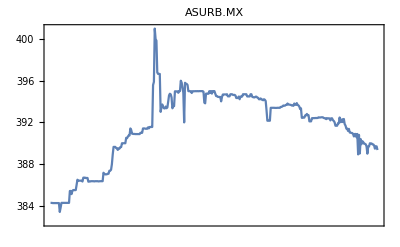
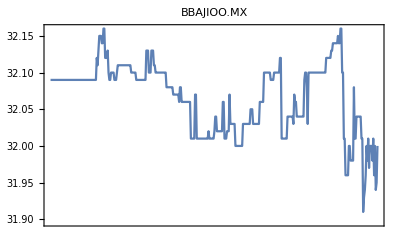
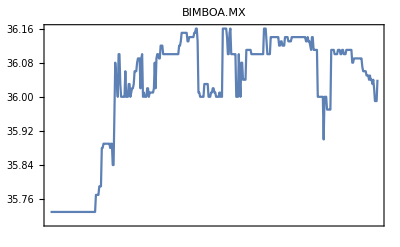
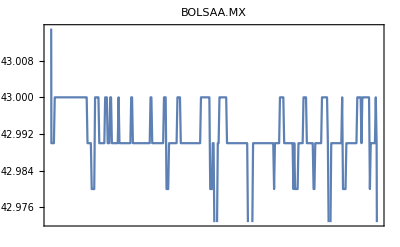

```mathematica
ProgressTable[
DateListPlot[Transpose[{onlyDates,onlyPrices[[All,i]]}],PlotLabel->stocks[[i]]],
{i,1,Length[stocks]}
]
```